# Kalman Folding versus Particle Filtering

Brian Beckman
16 Mar 2018

## Abstract

Kalman Folding is equivalent to Renormalized Recurrent Least Squares, and is Bayesian by construction (Beckman, 2018, https://goo.gl/CwLYjf). Therefore, it regularizes well. Sticking with concrete, numerical examples, we show that particle filtering can reproduce the results of Kalman Folding. For a more theoretical analysis, see Fernández-Villaverde (http://www.ssc.upenn.edu/~jesusfv/filters_format.pdf).

## Bishop’s Example

Chris Bishop’s Pattern Recognition and Machine Learning has an extended example fitting higher-order polynomials, linear in their coefficients, starting in section 1.1.

Bishop’s Training Set

Create a sequence of Ν=10 inputs for a training set, equally spaced in [0..1].

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[Ν_]:=Array[Identity,Ν,{0.,1.}];
```

Bishop’s ground truth is a single cycle of a sine wave. Add noise to a sample taken at the inputs of the training set above. Bishop doesn’t state an observation noise, but I guess σ_z=σ_t=0.30 to create a fake data set that resembles Bishop’s qualitatively.

Wolfram’s built-in NormalDistribution takes the standard deviation as its second argument, not the variance. Mixing up standard deviation and variance is an easy mistake. Bishop’s notation for normal distribution takes variance as second argument, so beware.

```mathematica
ClearAll[bishopTrainingSetY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopTrainingSetY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

Take a sample of the outputs and assign it the names bts for bishopTrainingSet. It isn’t his actual training set, which I didn’t find in print, just my simulation.

```mathematica
ClearAll[bishopTrainingSet,bts,bishopFake,bishopFakeSigma];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopTrainingSetY[xs,σ]},
{xs,ys}]];
bishopFakeSigma=0.30;
bishopTrainingSet=bts=bishopFake[10,bishopFakeSigma];
```

Make a plot like Bishop’s figure 1.7 (page 10).

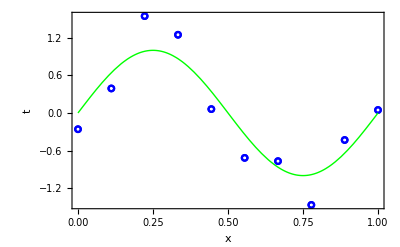

```mathematica
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set the scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* again to overdraw the plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

Partials: Gradients of the Unknown Parameters

Write a function for partials.

```mathematica
ClearAll[partialsFn];
partialsFn[order_,xs_]:=
Transpose@Quiet@Table[#^(i-1)/.{Indeterminate->1},{i,order+1}]&@xs;
```

A convenience function:

```mathematica
ClearAll[symbolicPowers];
symbolicPowers[variable_,order_]:=
partialsFn[order,{variable}]⟦1⟧;
```

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
{LinearSolve[Π,(sPΖiaᵀ.ζ+Λ.ξ)],Π}]];
```

```mathematica
ClearAll[rrlsFit];
rrlsFit[σ2ζ_,σ2ξ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2ξ^-1*IdentityMatrix[Μ+1]},
Module[{ξ,Λ},
{ξ,Λ}=Fold[
rlsUpdate[√σ2ζ IdentityMatrix[1]],
{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ];
{ξ/√σ2ζ,Λ}]]];
```

```mathematica
ClearAll[goodSolution];
```

```mathematica
Manipulate[Module[{x},
With[{σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
<|"σζ2"->σζ2,"σξ2"-> σξ2,"rrls⟦1⟧"->MatrixForm[goodSolution=rrls⟦1⟧]|>
]]],
Column[{
Button["RESET",(Μ=9;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]
```

```mathematica
Dynamic[goodSolution]
```

```mathematica
Manipulate[Module[{x},
With[{
terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧,
ts=bts⟦2⟧,
σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
With[{rrlsFn={terms}.rrls⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
AppendTo[showlist,Plot[rrlsFn,{x,0,1},PlotStyle->{Purple}]];Quiet@Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"ζ",""},{"ξ",Grid[{{"α: ",α,"β:",β}}]
}}]]]]]]],
Column[{
Button["RESET",(Μ=4;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,4,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ"},-7,3,Appearance->"Labeled"}]}]]
```

## Particle Filter

Each particle ξ^i,i∈[1.. N_s], is an (Μ+1)-vector guess at the state, i.e., the column vector of coefficients. There are N_s of them for each time tick in the simulation.

Initialization

```mathematica
ClearAll[σ0,P,P0,ξ0,ξ0s,importanceFunction];
ClearAll[Ns,σ0,σ,ξ,importanceFunctions,ξs,Μ,ws];

Ns=1000;

Μ=9;

σ0=10;
σ[0]=List/@ConstantArray[σ0,Μ+1];

ξ[0]=List/@ConstantArray[0.,Μ+1];

importanceFunctions[t_]:=
Table[
NormalDistribution[ξ[t]⟦i,1⟧,σ[t]⟦i,1⟧],
{i,Μ+1}];

ξs[0]=
Table[
ξ[0]⟦i,1⟧+RandomVariate[importanceFunctions[0]⟦i⟧],
{i,Μ+1},{j,Ns}];

Print[<|"σ"->σ,"Dimensions[ξs[0]]"->Dimensions[ξs[0]]|>];

ws[0]=ConstantArray[1./Ns,Ns];
Plus@@ws[0]
```

<|σ→σ,Dimensions[ξs[0]]→{10,1000}|>

1.

3D Point Clouds

```mathematica
ClearAll[threeDPointClouds];
threeDPointClouds[ξs_,σ_]:=
DynamicModule[{i=1,j=2,k=3},
Manipulate[Graphics3D[Point/@({ξs⟦i,All⟧,ξs⟦j,All⟧,ξs⟦k,All⟧}ᵀ),
Axes->True,AspectRatio->1,
AxesLabel->{"i: "<>ToString[i],"j: "<>ToString[j],"k: "<>ToString[k]},PlotRange->3{{-σ,σ},{-σ,σ},{-σ,σ}}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]},
{"k",SetterBar[Dynamic[k],Range[Μ+1]]}}]]];
threeDPointClouds[ξs[0],σ0]
```

Observations and Residuals

Observations are constant with time, but we include a time parameter for generality. The particle cloud changes with time due to resampling.

```mathematica
ClearAll[ξcol];
ξcol[t_,n_/;(1≤n≤Ns)]:=List/@ξs[t]⟦All,n⟧;
```

```mathematica
ClearAll[ζcol];
ζcol[t_]:=List/@bts⟦2⟧
```

```mathematica
ClearAll[residuals];
residuals[t_,n_/;1≤n≤Ns]:=
partialsFn[Μ,bts⟦1⟧].ξcol[t,n]-ζcol[t];
```

Sum of Squared Residuals (SSR)

```mathematica
ClearAll[ssr];
ssr[t_,n_/;1≤n≤Ns]:=(residuals[t,n]ᵀ.residuals[t,n])⟦1,1⟧;
```

```mathematica
ClearAll[ssrs];
(ssrs=ssr[0,#]&/@Range[Ns])//Short
```

{396.974,2425.15,«996»,3730.73,8448.51}

New Weights

Larger SSR means further from the observations. Let weights be inversely proportional to SSR, with divide-by-zero intentionally faulting because a zero SSR would signal an extremely improbable situation, most likely a bug somewhere else in the software.

```mathematica
(ws[1]= 1/ssrs/Plus@@(1/ssrs))//Short[#,3]&
```

{0.00137934,0.000225785,0.000226388,0.000831518,«992»,0.000295229,0.000255307,0.000146771,0.0000648118}

Check:

```mathematica
Plus@@ws[1]
```

1.

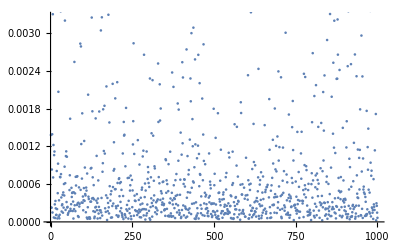

```mathematica
ListPlot[ws[1]]
```

Cull Particles

Keep only the particles that “do well” for the next time step, by some criterion driven by hyperparameters.

Pair each particle with its index:

```mathematica
ClearAll[indexedWeights];
(indexedWeights=MapThread[List,{Range[Ns],ws[1]}])//Short
```

{{1,0.00137934},«998»,{1000,0.0000648118}}

Keep the top p%. In general, p should be the reciprocal of an integer that divides N_s because we are going to copy each survivor 1/p times to make a new sample of size N_s.

```mathematica
ClearAll[p,sortedIndexedWeights,topPWeights,topPIndexedWeights,topPIndices,topPParticles];
p=0.10;
<|"sortedIndexedWeights"->((sortedIndexedWeights=Reverse@SortBy[indexedWeights,Last])//Short),
"topPIndexedWeights"->((topPIndexedWeights=sortedIndexedWeights⟦;;Floor[p Ns]⟧)//Short),
"topPWeights"->((topPWeights=Last/@topPIndexedWeights)//Short),
"topPIndices"->((topPIndices=First/@topPIndexedWeights)//Short),
"topPParticles//Dims"->((topPParticles=(ξs[0]⟦All,#⟧&/@topPIndices)ᵀ)//Dimensions),
"top 3 Particles"->(topPParticles⟦All,1;;3⟧//MatrixForm)|>
```

<|sortedIndexedWeights→{{261,0.0261222},«998»,{996,0.0000246449}},topPIndexedWeights→{{261,0.0261222},«98»,{697,0.00238918}},topPWeights→{0.0261222,0.0204499,«97»,0.00238918},topPIndices→{261,993,769,857,579,332,892,701,822,263,«80»,442,73,403,865,329,919,909,636,884,697},topPParticles//Dims→{10,100},top 3 Particles→(2.67859 | 1.55066 | 0.108888
-5.87824 | -6.15841 | -1.64365
1.92775 | 7.00917 | 2.37905
-2.19366 | -0.0571942 | 0.778594
6.67435 | 1.23859 | -1.24393
2.15711 | 5.17676 | 1.93329
0.311518 | -11.8938 | 13.6133
-3.37726 | -14.5866 | -4.67146
1.90699 | 7.31464 | 7.09674
-5.90205 | 6.37743 | -19.8817)|>

Structure emerges after culling.

```mathematica
threeDPointClouds[topPParticles,σ0]
```

Top p Particles

Replace each particle with 1/p copies, each perturbed by this new σ_1. There are other ways to compute an importance sample of the top p particles. One way, possibly biased, is to keep the original survivor and add 1/p-1 perturbed copies. We first perform this latter sample (original joined to three copies) to check matrix dimensions, but proceed with the former sample (four copies).

### Standard Deviations

```mathematica
ClearAll[σξ];
σξ[1]=StandardDeviation/@topPParticles
```

{3.58747,8.07821,7.84571,10.7471,9.28174,9.50718,9.38033,9.29126,8.63766,8.751}

Notice they’re all a little smaller than 100, which was the starting standard deviation. That’s good. It means that the culling process is picking particles more closely clumped.

```mathematica
ClearAll[conjColumns];
conjColumns[m1_,m2_]:=((m1ᵀ)~Join~(m2ᵀ))ᵀ;
```

### Unbiased? Importance Sample

```mathematica
ClearAll[make1OverP];
make1OverP[ξ_,σξ_,p_]:=
With[{n=Floor[1/p]},
Table[
RandomVariate[NormalDistribution[ξ⟦m⟧,σξ⟦m⟧],n],
{m,Μ+1}]];
make1OverP[topPParticles⟦All,41⟧,σξ[1],p]//MatrixForm
```

(2.90867 | 4.09692 | 7.10946 | 2.81627 | -0.679847 | -2.60687 | 5.44599 | 1.31342 | 7.09326 | -3.36762
-13.746 | -7.86086 | -3.77547 | -12.9327 | -15.0741 | -6.58088 | -4.07639 | -3.79023 | -15.2635 | -19.0812
8.85153 | -14.1702 | 11.2805 | -2.73396 | 0.258432 | -10.7311 | 4.98181 | 11.1411 | -11.2156 | -8.75609
15.9382 | -10.0601 | 8.80229 | 20.4942 | -4.70979 | 2.67061 | -5.72752 | 6.91352 | 1.53969 | -8.97069
17.4474 | -2.41551 | -19.7549 | -7.54275 | 2.95581 | 13.9782 | -2.70256 | -8.82277 | -5.21167 | -20.2729
21.4275 | 6.62622 | -14.3347 | 4.82215 | -1.78038 | 5.09944 | 11.4651 | 11.7416 | 5.14719 | 0.350314
11.3751 | 12.0701 | 10.1594 | 14.5411 | 6.32418 | 7.61915 | 21.3279 | 1.25149 | 18.5365 | 14.2961
-19.8345 | -21.4362 | -0.440683 | 7.08885 | -2.6392 | -5.17381 | -7.4081 | -3.56538 | -5.66502 | 3.33816
-14.3236 | -3.24764 | -7.64499 | 10.5251 | -12.389 | -11.2231 | -0.748998 | -4.44406 | -7.62614 | 12.1871
1.04035 | -0.659956 | -4.57397 | -3.56644 | 3.46029 | 9.25563 | -14.1968 | 3.44281 | 19.1923 | 18.9028)

New Particle Cloud

```mathematica
topPParticles//Dimensions
```

{10,100}

```mathematica
(ξs[1]=Fold[conjColumns,make1OverP[#,σξ[1],p]&/@(topPParticlesᵀ)])//Dimensions
```

{10,1000}

```mathematica
threeDPointClouds[ξs[1],σ0]
```

```mathematica
StandardDeviation/@ξs[0]
```

{9.87072,9.5836,9.82225,10.042,9.89986,10.2152,9.84507,9.66519,9.36036,10.0293}

```mathematica
StandardDeviation/@ξs[1]
```

{5.00311,11.2579,11.2038,15.035,13.12,13.8415,13.077,13.0164,12.2512,12.1753}

one goes down, the others go up.

Package and Experiment

Abstract the procedures above and iterate.

We have some global variables, namely Μ and N_s. Assert that input dimensions match expectations w.r.t. these globals.

Add a regularization parameter, λ, to penalize particles of large norm.

```mathematica
ClearAll[ssrFn,scalar,regula,weights,cull,iterate];
On[Assert];
scalar[m_]:=(
Assert[{1,1}===Dimensions[m]];
m⟦1,1⟧);
ssrFn[A_,ζ_]:=
Function[ξ,
With[{ress=ζ-A.ξ},
With[{ssr=ressᵀ.ress},
ssr]]];
regula[λ_][ξ_]:=(λ(ξ.ξ));
weights[xs_,ζ_,λ_][ξs_]:=
With[{A=partialsFn[Μ,xs]},
(Assert[Μ+1===Length[xs]];
Assert[Μ+1===Length[ζ]];
Assert[{Μ+1,Ns}===Dimensions[ξs]];
With[{cost=(regula[λ]/@(ξsᵀ))+(scalar/@ssrFn[A,ζ]/@(ξsᵀ))},
With[{ws= 1/cost/Plus@@(1/cost)},
Assert[Ns===Length[ws]];
Assert[Round[Plus@@ws,10.^-6]===1.];
ws]])];
cull[xs_,ζ_,λ_][p_,ξs_]:=Module[{indexedWeights,sortedIndexedWeights,topPIndexedWeights,topPWeights,topPIndices,topPParticles},
indexedWeights=Function[ws,MapThread[List,{Range[Ns],ws}]];
sortedIndexedWeights=Function[ws,Reverse@SortBy[indexedWeights[ws],Last]];
topPIndexedWeights=Function[ws,sortedIndexedWeights[ws]⟦;;Floor[p Ns]⟧];
topPIndices=Function[ws,First/@topPIndexedWeights[ws]];
topPParticles=Function[ws,
With[{result=(ξs⟦All,#⟧&/@topPIndices[ws])ᵀ},
Assert[{Μ+1,Floor[p Ns]}===Dimensions[result]];
result]];
topPParticles[weights[xs,ζ,λ][ξs]]];
iterate[xs_,ζ_,λ_][p_,ξs_]:=
With[{culled=cull[xs,ζ,λ][p,ξs]},
With[{σξ=StandardDeviation/@culled},
With[{result=Fold[conjColumns,make1OverP[#,σξ,p]&/@(culledᵀ)]},
Assert[{Μ+1,Ns}===Dimensions[result]];
result]]];
```

```mathematica
ClearAll[looseThreeDPointClouds];
looseThreeDPointClouds[ξs_]:=
DynamicModule[{i=1,j=2,k=3},
Manipulate[Graphics3D[Point/@({ξs⟦i,All⟧,ξs⟦j,All⟧,ξs⟦k,All⟧}ᵀ),
Axes->True,AspectRatio->1,
AxesLabel->{"i: "<>ToString[i],"j: "<>ToString[j],"k: "<>ToString[k]}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]},
{"k",SetterBar[Dynamic[k],Range[Μ+1]]}}]]];
```

```mathematica
(Fold[
iterate[bts⟦1⟧,List/@bts⟦2⟧,0.75][p,#1]&,
ξs[0],Range[200]])//looseThreeDPointClouds
```

```mathematica
Manipulate[
With[{top=
cull[bts⟦1⟧,List/@bts⟦2⟧,10.0^log10λ][0.05,
Fold[iterate[bts⟦1⟧,List/@bts⟦2⟧,10.0^log10λ][p,#1]&,ξs[0],Range[2^log2ℐ]]]},
Grid[{
{Module[{x},
With[{terms=symbolicPowers[x,Μ]},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0,1},PlotStyle->{Thick,Green}]}},
AppendTo[showlist,Plot[{terms}.goodSolution,{x,0,1},PlotStyle->{Purple}]];
AppendTo[showlist,Plot[terms.(Mean/@top),{x,0,1},PlotStyle->{Red}]];
Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"z",""},{"x",""}}]]]]],
Column[{ListLinePlot[{Mean/@top,Flatten[goodSolution]}],
ListLinePlot[StandardDeviation/@top]}]}
}]],
Grid[{{Button["RESET",(log10λ=0.0;log2ℐ=5)&],
Control[{{log10λ,0.00,"log_10λ"},-3.0,3.0,0.10,Appearance->{"Open","Labeled"}}]},
{"",Control[{{log2ℐ,5,"log_2ℐ"},0,10,1,Appearance->{"Open","Labeled"}}]}
}]]
```

## Conclusion